### FindRoot - Broyden’s Method

<summary>
Helper method to calculate an approximation of the Jacobian.
< /summary >
< param name = "f" > The function. < /param >
< param name = "x0" > The argument (initial guess). < /param >
< param name = "y0" > The result (of initial guess). < /param >

#### Calculate Approximate Jacobian

```mathematica
CalculateApproximateJacobian[f_,x0_,y0_]:=Module[
{dim,B,x,h,xj,y,i,j},
dim =Length[x0];
B=ConstantArray[0,{dim,dim}];
x=x0;

For[j=1,j≤ dim,j++,
h=Abs[x0[[j]]];
If[h==0,h=0.0001];

xj=x[[j]];
x[[j]]=xj+h;
y=f[x];
x[[j]]=xj;

For[i=1,i≤ dim,i++,
B[[i,j]]=(y[[i]]-y0[[i]])/h;
];
];
Return[B];
];
```

< summary > Find a solution of the equation f (x) = 0. < /summary >
< param name = "f" > The function to find roots from. < /param >
< param name = "initialGuess" > Initial guess of the root. < /param >
< param name = "accuracy" > Desired accuracy.The root will be refined until the accuracy or the maximum number of iterations is reached. < /param >
< param name = "maxIterations" > Maximum number of iterations.Usually 100. < /param >
< param name = "root" > The root that was found, if any.Undefined if the function returns false. < /param >
< returns > True if a root with the specified accuracy was found, else false. < /returns >

#### FindRoot

```mathematica
TryBroydenFindRoot[f_,initialGuess_, accuracy_, maxIterations_]:=Module[
{
x,y0,y,g,dx,xnew,ynew,gnew,B,g2,scale,root,dF,dB
},
x=initialGuess;

y0=f[initialGuess];
y=y0;
g=Norm[y];

B=CalculateApproximateJacobian[f,initialGuess,y0];

For[i=1,i≤ maxIterations,i++,
dx=-Inverse[B].y;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];

If[gnew>g,
g2=g*g;
scale=g2/(g2+gnew*gnew);
If[scale==0,scale=0.0001];

dx=scale*dx;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];
];

If[gnew<accuracy,
Return[{"Solution"->xnew,"Success"->True}];
];

dF=ynew-y;
dB=(dF-B.dx).(dx*1/(Norm[dx]^2));
B=B+dB;

x=xnew;
y=ynew;
g=gnew;
];
Print["Not Converge! Residue : "<>ToString[gnew]];
Return[{"Solution"->xnew,"Success"->False}];
];
```

#### Demo

```mathematica
F1[u_]:={u,1/5*u*u-10};
F2[v_]:={9,3}+v*{2,3};
EquaSet[x_]:=Module[
{x1,y1,x2,y2},
{x1,y1}=F1[x[[1]]];
{x2,y2}=F2[x[[2]]];
Return[{x1-x2,y1-y2}];
];
```

```mathematica
Ans="Solution"/.TryBroydenFindRoot[EquaSet,{0,0},0.00000001,100]
```

{0.349632,-4.32518}

{-5.4661×10^-10,1.79921×10^-9}

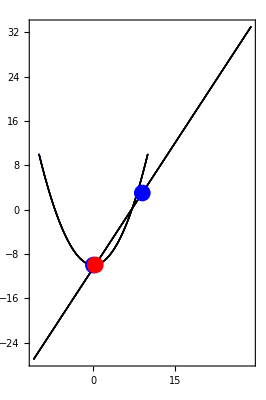

```mathematica
EquaSet[Ans]
Diagram1=ParametricPlot[{F1[u],F2[v]},{u,-10,10},{v,-10,10}];
AnsPlot=Graphics[{
Blue,PointSize-> 0.03,Point[F1[0]],
Blue,PointSize-> 0.03,Point[F2[0]],
Red,PointSize-> 0.03,Point[F1[Ans[[1]]]]
}];
Show[{Diagram1, AnsPlot}]
```

### Find Tangent Circle

#### Function

```mathematica
FindTangentCircle2D[curve1_,curveTangent1_,curve2_,curveTangent2_,initialCurvePara_,side_,radius_]:=Module[
{
iEqua,iResult,uui,ui1,ui2,pi,
TangentEqua,uu,u1,u2,p1,p2,O1,O2,
vvi,vv1,vv2,
StartAngle,EndAngle,midAngle,
Output
},
(*檢查2D輸入*)
If[Length[curve1[initialCurvePara[[1]]]]≠2,Return["curve1 needs to be 2D!"];];
If[Length[curveTangent1[initialCurvePara[[1]]]]≠2,Return["curveTangent1 needs to be 2D!"]];
If[Length[curve2[initialCurvePara[[2]]]]≠2,Return["curve2 needs to be 2D!"]];
If[Length[curveTangent2[initialCurvePara[[2]]]]≠2,Return["curveTangent2 needs to be 2D!"]];
If[Length[initialCurvePara],Return["initialCurvePara needs to be 2D!"]];
If[Length[side],Return["side needs to be 2D!"]];

(*求焦點*)
iEqua[para_]:=Module[
{
pp1,pp2
},
pp1=curve1[para[[1]]]//N;
pp2=curve2[para[[2]]]//N;
Return[pp1-pp2];
];
iResult=TryBroydenFindRoot[iEqua,initialCurvePara,10^-8,100];
If[("Success"/.iResult)== False,
Return["Have no intersection point between two Curves."];
];
uui="Solution"/.iResult;
ui1=uui[[1]];
ui2=uui[[2]];
pi=curve1[uui[[1]]];


(*求相切圓*)
TangentEqua[para_]:=Module[
{
tt1,tt2,
nn1,nn2,
eq1,eq2,eq3
},
p1=curve1[para[[1]]]//N;
p2=curve2[para[[2]]]//N;
tt1=curveTangent1[para[[1]]]//N;
tt2=curveTangent2[para[[2]]]//N;
nn1=Normalize[Take[Cross[{0,0,1},Join[tt1,{0}]]//N,2]];
nn2=Normalize[Take[Cross[{0,0,1},Join[tt2,{0}]]//N,2]];
vv1=side[[1]]*radius*nn1;
vv2=side[[2]]*radius*nn2;
O1=p1+vv1;
O2=p2+vv2;
(*uuc=Inverse[({{nn1[[1]], -nn2[[1]]}, {nn1[[2]], -nn2[[2]]}})].({{p2[[1]]-p1[[1]]}, {p2[[2]]-p1[[2]]}});
Origin=uuc[[1,1]]*nn1+p1;
rr1=Norm[p1-Origin];
rr2=Norm[p2-Origin];*)
Return[O1-O2];
];
uu="Solution"/.TryBroydenFindRoot[TangentEqua, initialCurvePara,10^-8,100];
u1=uu[[1]];
u2=uu[[2]];
vvi=O1-pi;
StartAngle=Pi+ArcTan[vv1[[1]],vv1[[2]]];
EndAngle=Pi+ArcTan[vv2[[1]],vv2[[2]]];
midAngle=Pi+ArcTan[vvi[[1]],vvi[[2]]];
If[(StartAngle-midAngle)*(EndAngle-midAngle)>0,
If[(StartAngle-midAngle)> (EndAngle-midAngle),
StartAngle=StartAngle-2*Pi;,
EndAngle=EndAngle-2*Pi;
];
];

Output={
"Center"->O1,
"Radius"-> radius,
"Angle"-> {StartAngle,EndAngle},
"U1"-> u1,
"U2"-> u2
};
Return[Output];
];
```

#### Demo

```mathematica
Curve1[u_]:={5*Cos[u],5*Sin[u]};
Tangent1[u_]:={5*Sin[u],-5*Cos[u]};
Curve2[u_]:={u,u*u};
Tangent2[u_]:={1,2u};
```

{Center→{1.54138,4.22778},Radius→0.5,StartAngle→1.22119,EndAngle→-0.241862,U1→1.22119,U2→2.02683}

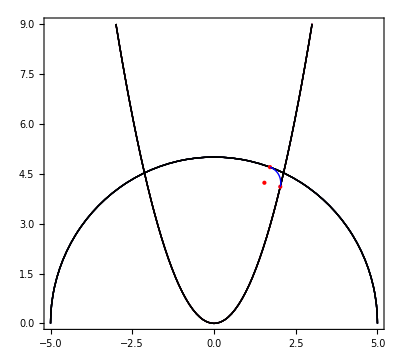

```mathematica
result=FindTangentCircle2D[Curve1,Tangent1,Curve2,Tangent2,{0.299*Pi,1.91},{-1,1},0.5]
questPlot=ParametricPlot[{Curve1[u1],Curve2[u2]},{u1,0,Pi},{u2,-3,3}];
vO="Center"/.result;
vr="Radius"/.result;
vStartAngle="StartAngle"/.result;
vEndAngle="EndAngle"/.result;
p1=Curve1["U1"/.result];
p2=Curve2["U2"/.result];
plot2=Graphics[{
Red,Point[{p1,p2,vO}],
Blue,Circle[vO,vr,{vStartAngle,vEndAngle}]
}];
Print[Show[{questPlot,plot2},PlotRange-> All]]
```